```mathematica
problem = Import["/home/2317101h/year_3/group_project/numerical_sol/section2.1/plates/laplace.dat"]

problem2 = ArrayReshape[problem, {100,100}]
```

{{100},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},9932,{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{-100}}
 |  |  |  |

{{100,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-100},98,{100,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,68,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-100}}
 |  |  |  |

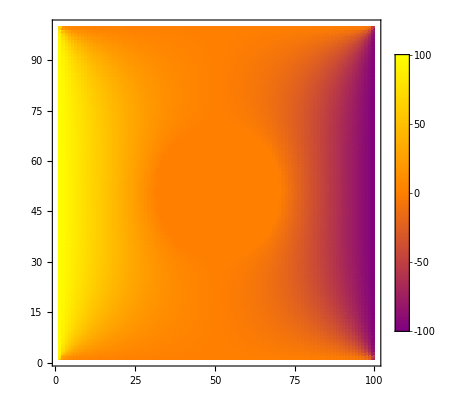

```mathematica
ListDensityPlot[problem2,PlotTheme->"Detailed",ColorFunction->(Blend[{Purple,Orange,Yellow},#1]&)]
```

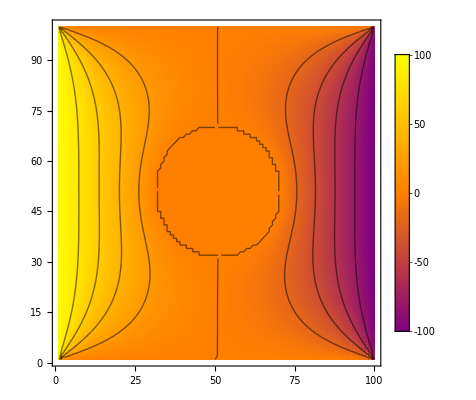

```mathematica
epilog=ListContourPlot[problem2,ContourShading->None][[1]];
ListDensityPlot[problem2,PlotTheme->"Detailed",ColorFunction->(Blend[{Purple,Orange,Yellow},#1]&), Epilog->epilog]
```